# Differential Non linear equation for periodic jumps.

This is differential equation is nonlinear and gives periodic jumps, it is described in the book:

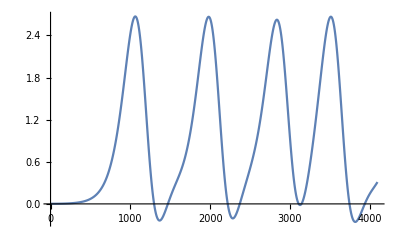

```mathematica
(* Irregular pulse - train generators after [Balmforth et. al. 1994]*)
m = N[1/Sqrt[2]];
c = 1.92847;
n  = 2;
len = 4096;
dt = 0.01;
x = Table[0,{len}];
pos = 0.002; jerk = accel = vel = 0.0;
Do [
jerk = -m accel - vel + c pos - pos^2;
accel += jerk * dt;
vel += accel * dt;
pos += vel * dt;
x[[q]] = pos,
{q,1, len}
];
ListPlot[x, Joined->True]
```

Solution using the Nonlinear Solve:

```mathematica
Clear[x]
```

```mathematica
μ = 1/√2; c = 1.92847;
```

```mathematica
sol = NDSolve[{x'''[t] == -μ x''[t]-x'[t]+c x[t]-x[t]^2, x''[0] == 0.0, x'[0] == 0.0, x[0] == 0.001}, {x}, {t,0,100}, MaxSteps->1000]
```

NDSolve::mxst: Maximum number of 1000 steps reached at the point t == 50.2151.

{{x→InterpolatingFunction[…]}}

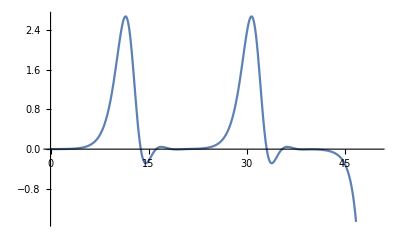

```mathematica
Plot[x[t]/.sol,{t,0,50}]
```